```mathematica
Solution=DSolve[p''[x]+a*p'[x]+p[x]*(b+c*Exp[-x*s])==d*Exp[-x*s],p[x],x]
```

{{p[x]→c^((a-√(a^2-4 b))/(2 s)+(√(a^2-4 b))/(2 s)) (ⅇ^(-s x))^((a-√(a^2-4 b))/(2 s)+(√(a^2-4 b))/(2 s)) s^(-(a-√(a^2-4 b))/s-(√(a^2-4 b))/s) BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s x)))/s] C[1] Gamma[1-(√(a^2-4 b))/s]+c^((a+√(a^2-4 b))/(2 s)-(√(a^2-4 b))/(2 s)) (ⅇ^(-s x))^((a+√(a^2-4 b))/(2 s)-(√(a^2-4 b))/(2 s)) s^(-(a+√(a^2-4 b))/s+(√(a^2-4 b))/s) BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s x)))/s] C[2] Gamma[1+(√(a^2-4 b))/s]+c^(a/(2 s)) (ⅇ^(-s x))^(a/(2 s)) s^(-a/s) (BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s x)))/s] Gamma[1+(√(a^2-4 b))/s] ∫_1^x -(c^(-a/(2 s)) d (ⅇ^(-s K[2]))^(1-a/(2 s)) s^(a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[2])))/s] Gamma[1-(√(a^2-4 b))/s])/(√(a^2-4 b))ⅆK[2]+BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s x)))/s] Gamma[1-(√(a^2-4 b))/s] ∫_1^x (c^(-a/(2 s)) d (ⅇ^(-s K[1]))^(1-a/(2 s)) s^(a/s) BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[1])))/s] Gamma[1+(√(a^2-4 b))/s])/(√(a^2-4 b))ⅆK[1])}}

```mathematica
Solution=First[First[Solution // FullSimplify]]
```

p[x]→c^(a/(2 s)) (ⅇ^(-s x))^(a/(2 s)) s^(-a/s) (BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s x)))/s] Gamma[(√(a^2-4 b)+s)/s] (C[2]+∫_1^x c^(-a/(2 s)) d (ⅇ^(-s K[2]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[2])))/s] Gamma[-(√(a^2-4 b))/s]ⅆK[2])+BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s x)))/s] Gamma[1-(√(a^2-4 b))/s] (C[1]+∫_1^x c^(-a/(2 s)) d (ⅇ^(-s K[1]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[1])))/s] Gamma[(√(a^2-4 b))/s]ⅆK[1]))

```mathematica
q[x_] := c^(a/(2 s)) (ⅇ^(-s x))^(a/(2 s)) s^(-a/s) (BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s x)))/s] Gamma[(√(a^2-4 b)+s)/s] (C[2]+∫_1^x c^(-a/(2 s)) d (ⅇ^(-s K[2]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[2])))/s] Gamma[-(√(a^2-4 b))/s]ⅆK[2])+BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s x)))/s] Gamma[1-(√(a^2-4 b))/s] (C[1]+∫_1^x c^(-a/(2 s)) d (ⅇ^(-s K[1]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[1])))/s] Gamma[(√(a^2-4 b))/s]ⅆK[1]));
```

```mathematica
{q[0]==0, q'[0]==0}
```

{c^(a/(2 s)) s^(-a/s) (BesselJ[(√(a^2-4 b))/s,(2 √c)/s] Gamma[(√(a^2-4 b)+s)/s] (C[2]+∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[2]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[2])))/s] Gamma[-(√(a^2-4 b))/s]ⅆK[2])+BesselJ[-(√(a^2-4 b))/s,(2 √c)/s] Gamma[1-(√(a^2-4 b))/s] (C[1]+∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[1]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[1])))/s] Gamma[(√(a^2-4 b))/s]ⅆK[1]))==0,c^(a/(2 s)) s^(-a/s) (c^(-a/(2 s)) d s^(-1+a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b))/s,(2 √c)/s] Gamma[1-(√(a^2-4 b))/s] Gamma[(√(a^2-4 b))/s]+c^(-a/(2 s)) d s^(-1+a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b))/s,(2 √c)/s] Gamma[-(√(a^2-4 b))/s] Gamma[(√(a^2-4 b)+s)/s]-1/2 √c (BesselJ[-1+(√(a^2-4 b))/s,(2 √c)/s]-BesselJ[1+(√(a^2-4 b))/s,(2 √c)/s]) Gamma[(√(a^2-4 b)+s)/s] (C[2]+∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[2]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[2])))/s] Gamma[-(√(a^2-4 b))/s]ⅆK[2])-1/2 √c (BesselJ[-1-(√(a^2-4 b))/s,(2 √c)/s]-BesselJ[1-(√(a^2-4 b))/s,(2 √c)/s]) Gamma[1-(√(a^2-4 b))/s] (C[1]+∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[1]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[1])))/s] Gamma[(√(a^2-4 b))/s]ⅆK[1]))-1/2 a c^(a/(2 s)) s^(-a/s) (BesselJ[(√(a^2-4 b))/s,(2 √c)/s] Gamma[(√(a^2-4 b)+s)/s] (C[2]+∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[2]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[2])))/s] Gamma[-(√(a^2-4 b))/s]ⅆK[2])+BesselJ[-(√(a^2-4 b))/s,(2 √c)/s] Gamma[1-(√(a^2-4 b))/s] (C[1]+∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[1]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[1])))/s] Gamma[(√(a^2-4 b))/s]ⅆK[1]))==0}

```mathematica
Solve[%, {C[1], C[2]}] // Simplify
```

{{C[1]→(c^(-(a+s)/(2 s)) (-2 d s^(a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b))/s,(2 √c)/s]^2 (Gamma[1-(√(a^2-4 b))/s] Gamma[(√(a^2-4 b))/s]+Gamma[-(√(a^2-4 b))/s] Gamma[(√(a^2-4 b)+s)/s])-c^((a+s)/(2 s)) s (BesselJ[-1+(√(a^2-4 b))/s,(2 √c)/s] BesselJ[-(√(a^2-4 b))/s,(2 √c)/s]+BesselJ[1-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b))/s,(2 √c)/s]-BesselJ[(√(a^2-4 b))/s,(2 √c)/s] BesselJ[-(√(a^2-4 b)+s)/s,(2 √c)/s]-BesselJ[-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b)+s)/s,(2 √c)/s]) Gamma[1-(√(a^2-4 b))/s] ∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[1]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[1])))/s] Gamma[(√(a^2-4 b))/s]ⅆK[1]))/(s (BesselJ[-1+(√(a^2-4 b))/s,(2 √c)/s] BesselJ[-(√(a^2-4 b))/s,(2 √c)/s]+BesselJ[1-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b))/s,(2 √c)/s]-BesselJ[(√(a^2-4 b))/s,(2 √c)/s] BesselJ[-(√(a^2-4 b)+s)/s,(2 √c)/s]-BesselJ[-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b)+s)/s,(2 √c)/s]) Gamma[1-(√(a^2-4 b))/s]),C[2]→(c^(-(a+s)/(2 s)) (2 d s^(a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c)/s]^2 BesselJ[(√(a^2-4 b))/s,(2 √c)/s] (Gamma[1-(√(a^2-4 b))/s] Gamma[(√(a^2-4 b))/s]+Gamma[-(√(a^2-4 b))/s] Gamma[(√(a^2-4 b)+s)/s])-c^((a+s)/(2 s)) s (BesselJ[-1+(√(a^2-4 b))/s,(2 √c)/s] BesselJ[-(√(a^2-4 b))/s,(2 √c)/s]+BesselJ[1-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b))/s,(2 √c)/s]-BesselJ[(√(a^2-4 b))/s,(2 √c)/s] BesselJ[-(√(a^2-4 b)+s)/s,(2 √c)/s]-BesselJ[-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b)+s)/s,(2 √c)/s]) Gamma[(√(a^2-4 b)+s)/s] ∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[2]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[2])))/s] Gamma[-(√(a^2-4 b))/s]ⅆK[2]))/(s (BesselJ[-1+(√(a^2-4 b))/s,(2 √c)/s] BesselJ[-(√(a^2-4 b))/s,(2 √c)/s]+BesselJ[1-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b))/s,(2 √c)/s]-BesselJ[(√(a^2-4 b))/s,(2 √c)/s] BesselJ[-(√(a^2-4 b)+s)/s,(2 √c)/s]-BesselJ[-(√(a^2-4 b))/s,(2 √c)/s] BesselJ[(√(a^2-4 b)+s)/s,(2 √c)/s]) Gamma[(√(a^2-4 b)+s)/s])}}

```mathematica
% // FullSimplify
```

{{C[1]→-∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[1]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[1])))/s] Gamma[(√(a^2-4 b))/s]ⅆK[1],C[2]→-∫_1^0 c^(-a/(2 s)) d (ⅇ^(-s K[2]))^(1-a/(2 s)) s^(-1+a/s) BesselJ[-(√(a^2-4 b))/s,(2 √c √(ⅇ^(-s K[2])))/s] Gamma[-(√(a^2-4 b))/s]ⅆK[2]}}

```mathematica
Solution=DSolve[p''[x]-(s/c-1)*p'[x]+p[x]*(s*r/c^2+w^2/n/c^2*x)==0, p[x], x]
```

{{p[x]→ⅇ^(-((c-s) x)/(2 c)) AiryAi[((c^2 n-2 c n s-4 n r s+n s^2)/(4 c^2 n)-(w^2 x)/(c^2 n))/((-w^2/(c^2 n))^(2/3))] C[1]+ⅇ^(-((c-s) x)/(2 c)) AiryBi[((c^2 n-2 c n s-4 n r s+n s^2)/(4 c^2 n)-(w^2 x)/(c^2 n))/((-w^2/(c^2 n))^(2/3))] C[2]}}

```mathematica
{a->11, c->1.2, n->3, e->3.5, w->8, r->1/1000}
```

```mathematica
Manipulate[
Sol=NDSolve[{p''[x]+a*p'[x]+a*r*p[x]+w^2/n*p[x]*Exp[-x*c]==10^3*w^2*e*Exp[-x*c], p[0]==0, p'[0]==0},  p[x],{x,0, 10}];
LogPlot[1-p[x]/n/e/10^3 /. Sol, {x,0,10}]
,{{a,11}, 1,100}, {{c,1.2},0.001,1}, {{n,3},1,1000}, {{e,3.5},2,5}, {{w,8},0.1,100}, {{r,1/1000}, 1/100000, 1/100}]
```

```mathematica
p[x] /. s /. x->0.1
```

{732.615}

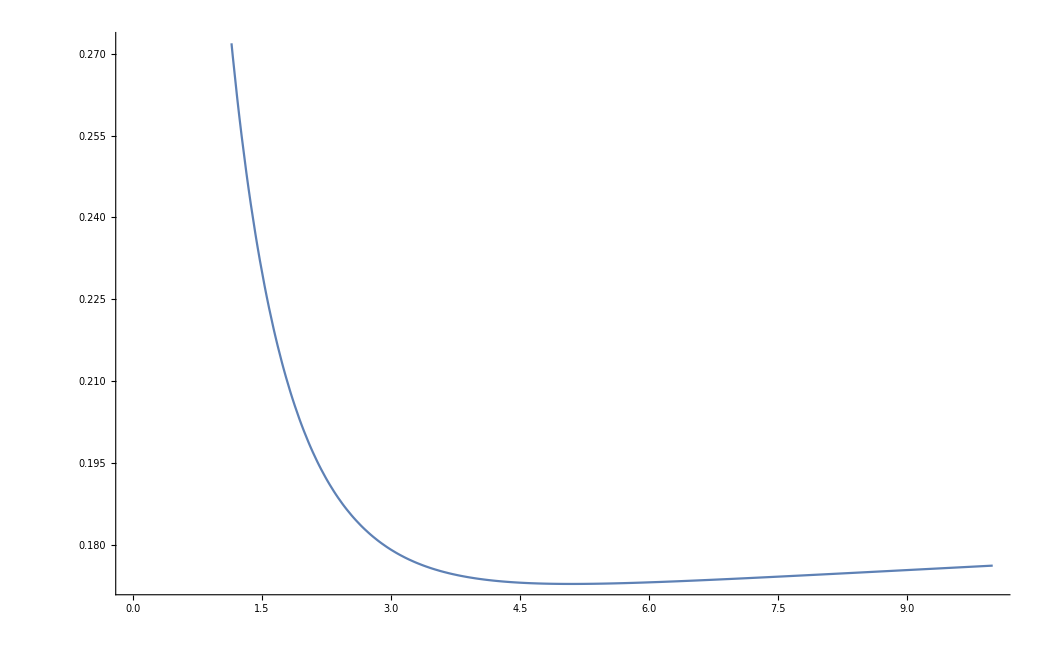

```mathematica
Plot[1-p[x]/3.5/3/10^3 /. s , {x,0, 10}]
```

```mathematica
Solution=DSolve[p''[x]*x^2-(a/c-1)*p'[x]*x+a*r/c^2*p[x]+w^2/n/c^2*p[x]*x==w^2*e/c^2*Subscript[Ε, 0]*x, p[x], x]
```

{{p[x]→c^(-(a-√a √(a-4 r))/c-(√a √(a-4 r))/c) n^(-(a-√a √(a-4 r))/(2 c)-(√a √(a-4 r))/(2 c)) w^((a-√a √(a-4 r))/c+(√a √(a-4 r))/c) x^((a-√a √(a-4 r))/(2 c)+(√a √(a-4 r))/(2 c)) BesselJ[-(√a √(a-4 r))/c,(2 w √x)/(c √n)] C[1] Gamma[1-(√a √(a-4 r))/c]+c^(-(a+√a √(a-4 r))/c+(√a √(a-4 r))/c) n^(-(a+√a √(a-4 r))/(2 c)+(√a √(a-4 r))/(2 c)) w^((a+√a √(a-4 r))/c-(√a √(a-4 r))/c) x^((a+√a √(a-4 r))/(2 c)-(√a √(a-4 r))/(2 c)) BesselJ[(√a √(a-4 r))/c,(2 w √x)/(c √n)] C[2] Gamma[1+(√a √(a-4 r))/c]-1/(√a c √(a-4 r))e w^2 ((w √x)/(c √n))^(-(√a √(a-4 r))/c) x Gamma[1-(√a √(a-4 r))/c] Gamma[1+(√a √(a-4 r))/c] (-BesselJ[(√a √(a-4 r))/c,(2 w √x)/(c √n)] Gamma[-(a-2 c+√a √(a-4 r))/(2 c)] HypergeometricPFQRegularized[{-(a-2 c+√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,-(a-4 c+√a √(a-4 r))/(2 c)},-(w^2 x)/(c^2 n)]+((w √x)/(c √n))^((2 √a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w √x)/(c √n)] Gamma[(-a+2 c+√a √(a-4 r))/(2 c)] HypergeometricPFQRegularized[{(-a+2 c+√a √(a-4 r))/(2 c)},{1+(√a √(a-4 r))/c,(-a+4 c+√a √(a-4 r))/(2 c)},-(w^2 x)/(c^2 n)]) Ε_0}}

```mathematica
Solution=Solution//FullSimplify
```

{{p[x]→c^(-a/c) n^(-a/(2 c)) w^(a/c) x^(a/(2 c)) (BesselJ[-(√a √(a-4 r))/c,(2 w √x)/(c √n)] C[1] Gamma[1-(√a √(a-4 r))/c]+BesselJ[(√a √(a-4 r))/c,(2 w √x)/(c √n)] C[2] Gamma[1+(√a √(a-4 r))/c])+1/(√a √(a-4 r))2 e w^2 x (-1/(a-2 c+√a √(a-4 r))Hypergeometric0F1[1+(√a √(a-4 r))/c,-(w^2 x)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-(w^2 x)/(c^2 n)]+1/(a-2 c-√a √(a-4 r))Hypergeometric0F1[1-(√a √(a-4 r))/c,-(w^2 x)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-(w^2 x)/(c^2 n)]) Ε_0}}

```mathematica
{{p[x]->c^(-a/c) n^(-a/(2 c)) w^(a/c) x^(a/(2 c)) (BesselJ[-(√a √(a-4 r))/c,(2 w √x)/(c √n)] C[1] Gamma[1-(√a √(a-4 r))/c]+BesselJ[(√a √(a-4 r))/c,(2 w √x)/(c √n)] C[2] Gamma[1+(√a √(a-4 r))/c])+1/(√a √(a-4 r))8 e w^2 x (-1/(a-2 c+√a √(a-4 r))Hypergeometric0F1[1+(√a √(a-4 r))/c,-(w^2 x)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-(w^2 x)/(c^2 n)]+1/(a-2 c-√a √(a-4 r))Hypergeometric0F1[1-(√a √(a-4 r))/c,-(w^2 x)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-(w^2 x)/(c^2 n)])}}
```

```mathematica
y[t_]= First[p[x] /. Solution /. x->t]
```

c^(-a/c) n^(-a/(2 c)) t^(a/(2 c)) w^(a/c) (BesselJ[-(√a √(a-4 r))/c,(2 √t w)/(c √n)] C[1] Gamma[1-(√a √(a-4 r))/c]+BesselJ[(√a √(a-4 r))/c,(2 √t w)/(c √n)] C[2] Gamma[1+(√a √(a-4 r))/c])+1/(√a √(a-4 r))2 e t w^2 (-1/(a-2 c+√a √(a-4 r))Hypergeometric0F1[1+(√a √(a-4 r))/c,-(t w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-(t w^2)/(c^2 n)]+1/(a-2 c-√a √(a-4 r))Hypergeometric0F1[1-(√a √(a-4 r))/c,-(t w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-(t w^2)/(c^2 n)]) Ε_0

```mathematica
yy[t_] = y[Exp[-t*c]];
```

```mathematica
CC = First[Solve[{yy[0]==0, yy'[0]==0},{C[1],C[2]}]] //Simplify
```

{C[1]→-((c^(a/c) e n^((a+c)/(2 c)) w^(1-a/c) (1/(√n (c^2+a (-c+r)))(w BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)]-w BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)]+a √n BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]) ((-a+2 c+√a √(a-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(a-2 c+√a √(a-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)])+4 BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] ((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-(w/(c √n))^((√a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+1/(n (a-2 c+√a √(a-4 r)) (c+√a √(a-4 r)))(√a n (a^(3/2)+a √(a-4 r)+c √(a-4 r)+√a (c-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]-1/(n (c-√a √(a-4 r)) (-a+2 c+√a √(a-4 r)))((-a^2 n+a^(3/2) n √(a-4 r)+√a c n √(a-4 r)-a n (c-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)])) Ε_0)/(2 √a √(a-4 r) (BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]-BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]+(-BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)]+BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)]) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]) Gamma[1-(√a √(a-4 r))/c])),C[2]→-((2 c^(a/c) e n^(1/2 (-1+a/c)) w^(1-a/c) (w/(c √n))^(-(√a √(a-4 r))/c) (4 n (c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (-BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+(w/(c √n))^((2 √a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)])+(w/(c √n))^((√a √(a-4 r))/c) (√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (-a^(3/2)+a √(a-4 r)-2 c √(a-4 r)+4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 (a^2-2 c^2-a^(3/2) √(a-4 r)+√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(w/(c √n))^((√a √(a-4 r))/c) (√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (a^(3/2)+a √(a-4 r)-2 c √(a-4 r)-4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 (a^2-2 c^2+a^(3/2) √(a-4 r)-√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]) Ε_0)/(√a (a-2 c+√a √(a-4 r)) (-c+√a √(a-4 r)) (c+√a √(a-4 r)) (-a+2 c+√a √(a-4 r)) √(a-4 r) (BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]-BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]+(-BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)]+BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)]) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]) Gamma[1+(√a √(a-4 r))/c]))}

```mathematica
z[t_] =(Subscript[Ε, 0]-yy[t]/e/n)/Subscript[Ε, 0] /. CC ;
```

```mathematica
zz[t_] = z[t] // Simplify
```

1/Ε_0(Ε_0-1/(2 √a n √(a-4 r))w (((ⅇ^(-c t))^(a/(2 c)) (-(((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^(-c t)) w)/(c √n)] (4 n (c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (-BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+(w/(c √n))^((2 √a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)])+(w/(c √n))^((√a √(a-4 r))/c) (√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (-a^(3/2)+a √(a-4 r)-2 c √(a-4 r)+4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 (a^2-2 c^2-a^(3/2) √(a-4 r)+√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(w/(c √n))^((√a √(a-4 r))/c) (√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (a^(3/2)+a √(a-4 r)-2 c √(a-4 r)-4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 (a^2-2 c^2+a^(3/2) √(a-4 r)-√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]))/(c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)))-n BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^(-c t)) w)/(c √n)] (1/(√n (c^2+a (-c+r)))(w BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)]-w BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)]+a √n BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]) ((-a+2 c+√a √(a-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(a-2 c+√a √(a-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)])+4 BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] ((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-(w/(c √n))^((√a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+1/(n (a-2 c+√a √(a-4 r)) (c+√a √(a-4 r)))(√a n (a^(3/2)+a √(a-4 r)+c √(a-4 r)+√a (c-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]-1/(n (c-√a √(a-4 r)) (-a+2 c+√a √(a-4 r)))((-a^2 n+a^(3/2) n √(a-4 r)+√a c n √(a-4 r)-a n (c-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]))))/(√n (BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]-BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]+(-BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)]+BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)]) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]))+4 ⅇ^(-c t) w (-(Hypergeometric0F1[1+(√a √(a-4 r))/c,-(ⅇ^(-c t) w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-(ⅇ^(-c t) w^2)/(c^2 n)])/(a-2 c+√a √(a-4 r))+(Hypergeometric0F1[1-(√a √(a-4 r))/c,-(ⅇ^(-c t) w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-(ⅇ^(-c t) w^2)/(c^2 n)])/(a-2 c-√a √(a-4 r)))) Ε_0)

```mathematica
Simplified=Series[Log[zz[t]], {t,1,1}]
```

Log[1/4 (4-1/(√a n √(a-4 r))2 w (((ⅇ^-c)^(a/(2 c)) (-(((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)] (4 n (c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (-BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+(w/(c √n))^((2 √a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)])+(w/(c √n))^((√a √(a-4 r))/c) (√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (-a^(3/2)+a √(a-4 r)-2 c √(a-4 r)+4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 (a^2-2 c^2-a^(3/2) √(a-4 r)+√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(w/(c √n))^((√a √(a-4 r))/c) (√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (a^(3/2)+a √(a-4 r)-2 c √(a-4 r)-4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 (a^2-2 c^2+a^(3/2) √(a-4 r)-√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]))/(c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)))-n BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)] (1/(√n (c^2+a (-c+r)))(w BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)]-w BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)]+a √n BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]) ((-a+2 c+√a √(a-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(a-2 c+√a √(a-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)])+4 BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] ((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-(w/(c √n))^((√a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+1/(n (a-2 c+√a √(a-4 r)) (c+√a √(a-4 r)))(√a n (a^(3/2)+a √(a-4 r)+c √(a-4 r)+√a (c-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]-1/(n (c-√a √(a-4 r)) (-a+2 c+√a √(a-4 r)))((-a^2 n+a^(3/2) n √(a-4 r)+√a c n √(a-4 r)-a n (c-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]))))/(√n (BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]-BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]+(-BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)]+BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)]) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]))+4 ⅇ^-c w (-(Hypergeometric0F1[1+(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-(ⅇ^-c w^2)/(c^2 n)])/(a-2 c+√a √(a-4 r))+(Hypergeometric0F1[1-(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-(ⅇ^-c w^2)/(c^2 n)])/(a-2 c-√a √(a-4 r)))))]-(2 (w ((-1/2 a (ⅇ^-c)^(a/(2 c)) (-(((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)] (4 n (c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (-BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+(w/(c √n))^((2 √a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)])+(w/(c √n))^((√a √(a-4 r))/c) (√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (-a^(3/2)+a √(a-4 r)-2 c √(a-4 r)+4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 (a^2-2 c^2-a^(3/2) √(a-4 r)+√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(w/(c √n))^((√a √(a-4 r))/c) (√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (a^(3/2)+a √(a-4 r)-2 c √(a-4 r)-4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 (a^2-2 c^2+a^(3/2) √(a-4 r)-√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]))/(c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)))-n BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)] (1/(√n (c^2+a (-c+r)))(w BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)]-w BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)]+a √n BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]) ((-a+2 c+√a √(a-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(a-2 c+√a √(a-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)])+4 BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] ((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-(w/(c √n))^((√a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+1/(n (a-2 c+√a √(a-4 r)) (c+√a √(a-4 r)))(√a n (a^(3/2)+a √(a-4 r)+c √(a-4 r)+√a (c-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]-1/(n (c-√a √(a-4 r)) (-a+2 c+√a √(a-4 r)))((-a^2 n+a^(3/2) n √(a-4 r)+√a c n √(a-4 r)-a n (c-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)])))+(ⅇ^-c)^(a/(2 c)) ((√(ⅇ^-c) w (w/(c √n))^(-(√a √(a-4 r))/c) (-BesselJ[1+(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)]+(√a √n √(a-4 r) BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)])/(2 √(ⅇ^-c) w)) (4 n (c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (-BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+(w/(c √n))^((2 √a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)])+(w/(c √n))^((√a √(a-4 r))/c) (√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (-a^(3/2)+a √(a-4 r)-2 c √(a-4 r)+4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 (a^2-2 c^2-a^(3/2) √(a-4 r)+√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(w/(c √n))^((√a √(a-4 r))/c) (√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (a^(3/2)+a √(a-4 r)-2 c √(a-4 r)-4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 (a^2-2 c^2+a^(3/2) √(a-4 r)-√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]))/(√n (c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)))+√(ⅇ^-c) √n w (-BesselJ[1-(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)]-(√a √n √(a-4 r) BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)])/(2 √(ⅇ^-c) w)) (1/(√n (c^2+a (-c+r)))(w BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)]-w BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)]+a √n BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]) ((-a+2 c+√a √(a-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(a-2 c+√a √(a-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)])+4 BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] ((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-(w/(c √n))^((√a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+1/(n (a-2 c+√a √(a-4 r)) (c+√a √(a-4 r)))(√a n (a^(3/2)+a √(a-4 r)+c √(a-4 r)+√a (c-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]-1/(n (c-√a √(a-4 r)) (-a+2 c+√a √(a-4 r)))((-a^2 n+a^(3/2) n √(a-4 r)+√a c n √(a-4 r)-a n (c-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]))))/(√n (BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]-BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]+(-BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)]+BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)]) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]))+4 w (-c ⅇ^-c (-(Hypergeometric0F1[1+(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-(ⅇ^-c w^2)/(c^2 n)])/(a-2 c+√a √(a-4 r))+(Hypergeometric0F1[1-(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-(ⅇ^-c w^2)/(c^2 n)])/(a-2 c-√a √(a-4 r)))+ⅇ^-c (1/(a-2 c+√a √(a-4 r))(-(ⅇ^-c w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-(ⅇ^-c w^2)/(c^2 n)])/(n (c+√a √(a-4 r)))-(ⅇ^-c (-a+2 c-√a √(a-4 r)) w^2 Hypergeometric0F1[1+(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{2-a/(2 c)-(√a √(a-4 r))/(2 c)},{2-(√a √(a-4 r))/c,3-a/(2 c)-(√a √(a-4 r))/(2 c)},-(ⅇ^-c w^2)/(c^2 n)])/(n (c-√a √(a-4 r)) (-a+4 c-√a √(a-4 r))))+1/(a-2 c-√a √(a-4 r))((ⅇ^-c w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-(ⅇ^-c w^2)/(c^2 n)])/(n (c-√a √(a-4 r)))+(ⅇ^-c (-a+2 c+√a √(a-4 r)) w^2 Hypergeometric0F1[1-(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{2-a/(2 c)+(√a √(a-4 r))/(2 c)},{3-a/(2 c)+(√a √(a-4 r))/(2 c),2+(√a √(a-4 r))/c},-(ⅇ^-c w^2)/(c^2 n)])/(n (c+√a √(a-4 r)) (-a+4 c+√a √(a-4 r)))))))) (t-1))/(√a n √(a-4 r) (4-1/(√a n √(a-4 r))2 w (((ⅇ^-c)^(a/(2 c)) (-(((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)] (4 n (c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (-BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+(w/(c √n))^((2 √a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)])+(w/(c √n))^((√a √(a-4 r))/c) (√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (-a+2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (-a^(3/2)+a √(a-4 r)-2 c √(a-4 r)+4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 (a^2-2 c^2-a^(3/2) √(a-4 r)+√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(w/(c √n))^((√a √(a-4 r))/c) (√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-√n (a-2 c+√a √(a-4 r)) (a^2-c^2-4 a r) w BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] (√a n (a^(3/2)+a √(a-4 r)-2 c √(a-4 r)-4 √a r) (a^2-c^2-4 a r) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 (a^2-2 c^2+a^(3/2) √(a-4 r)-√a c √(a-4 r)+a (c-4 r)) w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)])) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]))/(c^4-a c^2 (c-5 r)+a^3 (c-r)-a^2 (c^2+4 c r-4 r^2)))-n BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^-c) w)/(c √n)] (1/(√n (c^2+a (-c+r)))(w BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)]-w BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)]+a √n BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]) ((-a+2 c+√a √(a-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]+(a-2 c+√a √(a-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)])+4 BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] ((w/(c √n))^(-(√a √(a-4 r))/c) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1+(√a √(a-4 r))/c] Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]-(w/(c √n))^((√a √(a-4 r))/c) BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)] Gamma[1-(√a √(a-4 r))/c] Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]+1/(n (a-2 c+√a √(a-4 r)) (c+√a √(a-4 r)))(√a n (a^(3/2)+a √(a-4 r)+c √(a-4 r)+√a (c-4 r)) Hypergeometric0F1[1+(√a √(a-4 r))/c,-w^2/(c^2 n)]-2 w^2 Hypergeometric0F1[2+(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-w^2/(c^2 n)]-1/(n (c-√a √(a-4 r)) (-a+2 c+√a √(a-4 r)))((-a^2 n+a^(3/2) n √(a-4 r)+√a c n √(a-4 r)-a n (c-4 r)) Hypergeometric0F1[1-(√a √(a-4 r))/c,-w^2/(c^2 n)]+2 w^2 Hypergeometric0F1[2-(√a √(a-4 r))/c,-w^2/(c^2 n)]) HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-w^2/(c^2 n)]))))/(√n (BesselJ[-1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]-BesselJ[1+(√a √(a-4 r))/c,(2 w)/(c √n)] BesselJ[-(√a √(a-4 r))/c,(2 w)/(c √n)]+(-BesselJ[-(c+√a √(a-4 r))/c,(2 w)/(c √n)]+BesselJ[1-(√a √(a-4 r))/c,(2 w)/(c √n)]) BesselJ[(√a √(a-4 r))/c,(2 w)/(c √n)]))+4 ⅇ^-c w (-(Hypergeometric0F1[1+(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)-(√a √(a-4 r))/(2 c)},{1-(√a √(a-4 r))/c,2-a/(2 c)-(√a √(a-4 r))/(2 c)},-(ⅇ^-c w^2)/(c^2 n)])/(a-2 c+√a √(a-4 r))+(Hypergeometric0F1[1-(√a √(a-4 r))/c,-(ⅇ^-c w^2)/(c^2 n)] HypergeometricPFQ[{1-a/(2 c)+(√a √(a-4 r))/(2 c)},{2-a/(2 c)+(√a √(a-4 r))/(2 c),1+(√a √(a-4 r))/c},-(ⅇ^-c w^2)/(c^2 n)])/(a-2 c-√a √(a-4 r))))))+O[t-1]^2

```mathematica
Series[Normal[Simplified], {w,6,2}] // Simplify
```

$Aborted

```mathematica
Simplified /. {a->24.4, c->0.088, n->6, e->3.5, w->18, r->1/10000} // Simplify
```

-2.22922-2.23334 (t-1)+O[t-1]^2

```mathematica
zzz[t_] =  zz[t] /. {a->24.4, c->0.088, n->6, e->3.5, w->9, r->1/10000} ;
```

```mathematica
zzw[cc_,t_] =  zz[t] /. {a->24.4, c->cc, n->6, e->3.5, w->9, r->1/10000} ;
```

```mathematica
D[Log[zzz[t]],t]  // Simplify
```

zz'[t]/zz[t]

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
D[Log[zzz[t]],t] /. t->1 // Simplify
```

zz'[1]/zz[1]

```mathematica
Manipulate[Plot[Log[zzw[c,t]], {c, 0.01, 0.1}, PlotPoints->20, MaxRecursion->0 ], {{t,1},0,10}]
```

```mathematica
DSolve[x^2 l''[x] + x l'[x] + (x^2+9/16) l[x] == 0, l[x], x]
```

{{l[x]→BesselJ[(3 ⅈ)/4,x] C[1]+BesselY[(3 ⅈ)/4,x] C[2]}}